```mathematica
(*quiccroot="/home/philippe/Documents/EPM/QuICC/build/QuICC_aquad/serial";*)
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];

Needs["NumericalDifferentialEquationAnalysis`"]
$MaxExtraPrecision=1000;
mpprec=100;
Plm[l_,m_,t_]:=LegendreP[l,m,t]/(√(2π(2(l+m)!)/((2l+1)(l-m)!)))
dLegendreP[l_,m_,t_]=D[LegendreP[l,m,t],t];
d2LegendreP[l_,m_,t_]=D[LegendreP[l,m,t],{t,2}];
dPlm[l_,m_,t_]:=-√(1-t^2)dLegendreP[l,m,t]/(√(2π(2(l+m)!)/((2l+1)(l-m)!)))
d2Plm[l_,m_,t_]:=(-t dLegendreP[l,m,t]+(1-t^2)d2LegendreP[l,m,t])/(√(2π(2(l+m)!)/((2l+1)(l-m)!)))
divsinPlm[l_,m_,t_]:=If[m==0,0t,1/(√(1-t^2))LegendreP[l,m,t]/(√(2π(2(l+m)!)/((2l+1)(l-m)!)))]
lgrid[n_]:=If[ToExpression["ValueQ[lgrid"<>ToString[n]<>"]"],ToExpression["lgrid"<>ToString[n]],ToExpression["Set[lgrid"<>ToString[n]<>",GaussianQuadratureWeights["<>ToString[n]<>",-1,1,mpprec][[;;,1]]]"]];
lweights[n_]:=If[ToExpression["ValueQ[lweights"<>ToString[n]<>"]"],ToExpression["lweights"<>ToString[n]],ToExpression["Set[lweights"<>ToString[n]<>",GaussianQuadratureWeights["<>ToString[n]<>",-1,1,mpprec][[;;,2]]]"]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","Polynomial","TestSuite"}]];
datadir={"data","Polynomial","ALegendre"}; (*data or _data?*)
refdir={"_refdata","Polynomial","ALegendre"}; (*ref or _refdata?*)
```

```mathematica
refop[ns_,gfunc_,wfunc_,opfunc_,name_]:= Module[{outprec = 16,i,specN,gridN,m, grid,weights, op,msg,tempmsg,fname},
For[i = 1, i≤ Length[ns],i++,
specN=ns[[i,1]];
gridN = ns[[i,2]];
m=ns[[i,3]];
msg="Exporting "<>name<>" ALegendre operator for N = "<>ToString[specN]<>", Ng = " <>ToString[gridN]<>", m = "<>ToString[m]<>"...";
tempmsg=PrintTemporary[msg];
grid = gfunc[gridN];
weights = wfunc[gridN];
op=Transpose[Table[opfunc[l,m,grid],{l,m,m+specN-1}]];
(*Print[op];*)

op = N[op,outprec];
fname=name<>"_m"<>ToString[m]<>"_l"<>ToString[specN]<>"_g"<>ToString[gridN]<>".dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],op];
fname="weighted_"<>fname;
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],weights*op];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
]
```

The first two are step-by-step tests to check everything is right at every meaningful iteration

```mathematica
refop[{{1,16,0},{2,16,0},{3,16,0},{4,16,0},{16,16,0},{128,16,0},
{1,16,1},{2,16,1},{3,16,1},{4,16,1},{5,16,1},{16,16,1},
{1,16,2},{2,16,2},{3,16,2},{4,16,2}, {16,16,2},
{128,16,20}, {128,16,128}},lgrid,lweights,dPlm,"dPlm"];
```

Exporting dPlm ALegendre operator for N = 1, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:35)

Exporting dPlm ALegendre operator for N = 2, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:35)

Exporting dPlm ALegendre operator for N = 3, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:35)

Exporting dPlm ALegendre operator for N = 4, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:35)

Exporting dPlm ALegendre operator for N = 16, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:35)

Exporting dPlm ALegendre operator for N = 128, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 1, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 2, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 3, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 4, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 5, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 1, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 2, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 3, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 4, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:36)

Exporting dPlm ALegendre operator for N = 128, Ng = 16, m = 20... Done(Sun 15 Jun 2025 11:43:37)

Exporting dPlm ALegendre operator for N = 128, Ng = 16, m = 128... Done(Sun 15 Jun 2025 11:43:37)

```mathematica
refop[{{1,16,0},{2,16,0},{3,16,0},{4,16,0},{16,16,0},{128,16,0},
{1,16,1},{2,16,1},{3,16,1},{4,16,1},{5,16,1},
{1,16,2},{2,16,2},{3,16,2},{4,16,2},
{128,16,20}, {128,16,128}},lgrid,lweights,d2Plm,"d2Plm"];
```

Exporting d2Plm ALegendre operator for N = 1, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:29)

Exporting d2Plm ALegendre operator for N = 2, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:29)

Exporting d2Plm ALegendre operator for N = 3, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:29)

Exporting d2Plm ALegendre operator for N = 4, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:29)

Exporting d2Plm ALegendre operator for N = 16, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:30)

Exporting d2Plm ALegendre operator for N = 128, Ng = 16, m = 0... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 1, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 2, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 3, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 4, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 5, Ng = 16, m = 1... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 1, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 2, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 3, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 4, Ng = 16, m = 2... Done(Sun 15 Jun 2025 11:43:31)

Exporting d2Plm ALegendre operator for N = 128, Ng = 16, m = 20... Done(Sun 15 Jun 2025 11:43:32)

Exporting d2Plm ALegendre operator for N = 128, Ng = 16, m = 128... Done(Sun 15 Jun 2025 11:43:33)

```mathematica
refop[{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}},lgrid,lweights,Plm,"Plm"];
```

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 0... Done(Fri 13 Jun 2025 14:00:46)

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 1... Done(Fri 13 Jun 2025 14:00:54)

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 2... Done(Fri 13 Jun 2025 14:01:00)

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 5... Done(Fri 13 Jun 2025 14:01:06)

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 20... Done(Fri 13 Jun 2025 14:01:11)

Exporting Plm ALegendre operator for N = 128, Ng = 256, m = 128... Done(Fri 13 Jun 2025 14:01:16)

```mathematica
refop[{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}},lgrid,lweights,dPlm,"dPlm"];
```

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 0... Done(Fri 13 Jun 2025 13:43:43)

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 1... Done(Fri 13 Jun 2025 13:43:54)

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 2... Done(Fri 13 Jun 2025 13:44:02)

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 5... Done(Fri 13 Jun 2025 13:44:10)

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 20... Done(Fri 13 Jun 2025 13:44:19)

Exporting dPlm ALegendre operator for N = 128, Ng = 256, m = 128... Done(Fri 13 Jun 2025 13:44:27)

```mathematica
refop[{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}},lgrid,lweights,d2Plm,"d2Plm"];
```

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 0... Done(Fri 13 Jun 2025 13:41:43)

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 1... Done(Fri 13 Jun 2025 13:41:59)

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 2... Done(Fri 13 Jun 2025 13:42:15)

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 5... Done(Fri 13 Jun 2025 13:42:32)

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 20... Done(Fri 13 Jun 2025 13:42:48)

Exporting d2Plm ALegendre operator for N = 128, Ng = 256, m = 128... Done(Fri 13 Jun 2025 13:43:04)

```mathematica
refop[{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}},lgrid,lweights,divsinPlm,"sin_1Plm"];
```

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 0... Done(Fri 13 Jun 2025 13:25:38)

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 1... Done(Fri 13 Jun 2025 13:25:42)

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 2... Done(Fri 13 Jun 2025 13:25:46)

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 5... Done(Fri 13 Jun 2025 13:25:50)

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 20... Done(Fri 13 Jun 2025 13:25:55)

Exporting sin_1Plm ALegendre operator for N = 128, Ng = 256, m = 128... Done(Fri 13 Jun 2025 13:25:59)

```mathematica
dataroot
```

/Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/Plm_m0_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

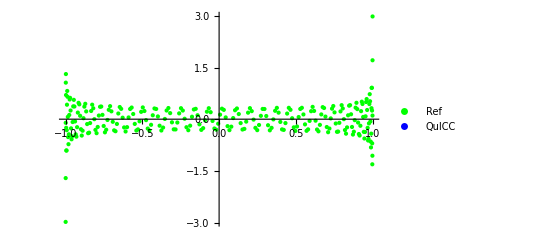

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=00;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/Plm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
l=m+69;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,Plm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,l,y,pts,ref,err,relerr,pl1,pl2]
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/dPlm_m0_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

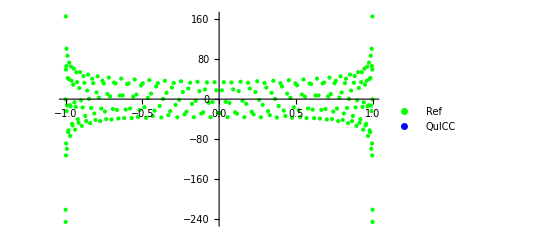

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=0;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/dPlm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
l=m+113;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,dPlm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,l,y,pts,ref,err,relerr,pl1,pl2]
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/sin_1Plm_m1_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

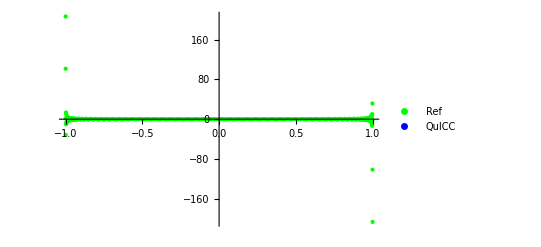

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=01;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/sin_1Plm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
l=m+111;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,divsinPlm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,l,y,pts,ref,err,relerr,pl1,pl2]
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/weighted_Plm_m0_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

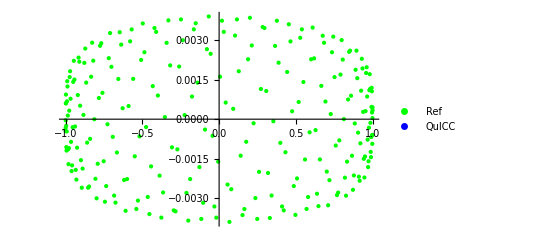

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=00;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/weighted_Plm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
weights=lweights[gridN];
l=m+69;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights Plm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,weights,l,y,pts,ref,err,relerr,pl1,pl2]
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/weighted_dPlm_m0_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

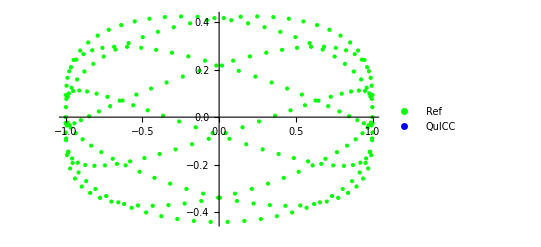

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=0;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/weighted_dPlm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
weights=lweights[gridN];
l=m+113;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights dPlm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,weights,l,y,pts,ref,err,relerr,pl1,pl2]
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver/build/Components/Polynomial/TestSuite/data/Polynomial/ALegendre/weighted_sin_1Plm_m1_l128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«19»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

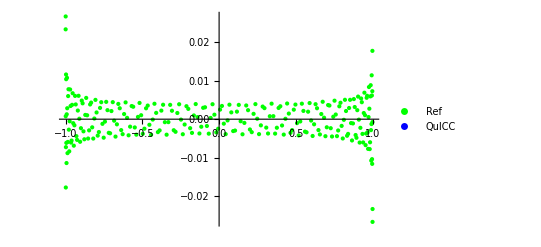

```mathematica
Clear[data]
maxL=128;
gridN=256;
m=01;
Quiet[data=ReadList[dataroot<>"/data/Polynomial/ALegendre/weighted_sin_1Plm_m"<>ToString[m]<>"_l"<>ToString[maxL]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=lgrid[gridN];
weights = lweights[gridN];
l=m+111;
y=data[[;;,l-m+1]];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*divsinPlm[l,m,grid]],2];
err = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
Clear[maxL,gridN,m,grid,weights,l,y,pts,ref,err,relerr,pl1,pl2]
```